# 1-D universal estimator using DNN

## Generating data (without duplicating θ and logging the histogram)

Generates synthetic data for DNN :

Arguments:
	n: number of samples drawn for a given θ 
	M: number of different θ generated in the range [min_θ, max_θ]
	f: the distribution function for generating samples. f(θ, N) returns N observations using parameter θ
	range: range of the dist parameter θ
	bins: number of bins in the histograms generated from samples
Return:
	a table of associations(one row per sample): histogram->θ

```mathematica
GenerateData[M_, n_, f_, range_, bins_:-1]:=
	Module[{params, samples, nbins, MAXBINS},
		params=Table[RandomReal[{range[[1]],range[[2]]}],{i,1,M}];
		(*generate M different random initparameters in the range [min_θ,max_θ]*) 
		samples=Table[f[params[[i]],n],{i,1,M}];
		(*generate M distributions, each distribution has n number/data*, now we have M*n data*)
		MAXBINS=10000;
		nbins=If[bins>0,bins,Min[MAXBINS, Ceiling[Max[samples]]+1](*Ceiling[Max[samples]]+2] if using zero padding*)];
		h[x_]:=HistogramList[x,{0,nbins,1}][[2]]; (*without using log10(x+1)*)
		Table[h@samples[[i]]->params[[i]], {i,1,M}]  
	
	]
```

## Example of generated data

```mathematica
(*f[å_,N_]:=RandomVariate[WaringYuleDistribution[å],N];
Print[GenerateData[5,10,f,{2,3}]//TableForm];*)
```

{6,3,0,1}→2.67938
{6,0,4,0}→2.21798
{7,1,1,1}→2.25193
{7,2,1,0}→2.76568
{6,1,1,2}→2.16986

## DNN

Generate a DNN for predicting the parameter θ from the distribution histogram
The input size is the number of bins in the input histogram, the output is a scalar predicting the parameter used to generate the input sample.

```mathematica
CreateNet[bins_]:=( 
NetChain[{
LinearLayer[bins],  
BatchNormalizationLayer[],  (*batch normaliztiozion*)
ElementwiseLayer[Ramp], (*Ramp is the relu*)

LinearLayer[bins], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp], 

LinearLayer[bins], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp], 

LinearLayer[1]
},
"Input"->bins, 
"Output" -> "Scalar"]
)
```

## 1-D universal estimator using DNN

Given a distribution  dist(x|θ) and the range for the parameter θ,  
UniversalEstimator returns an Estimator function for predicting the parameter θ given an input sample S.

```mathematica
UniversalEstimator[dist_, range_]:=Module[{g, M, n, trainSet, bins, valSet ,net, trained, model, h},
(*define a sample generator*)
g[θ_,n_] := RandomVariate[dist[θ],n];

(*train a NN for predicting the parameter θ *)
(*generate learning samples in the the given parameter range*)
M = 10000; 
n = 10240;   (*number of observations in each sample*)
trainSet=GenerateData[M,n, g, range];
bins = Length@trainSet[[1]][[1]]; (*use the same number of bins for the validation set*)
valSet=GenerateData[M/2,n, g, range, bins];

(*Create and train the NN*)
net = NetInitialize@CreateNet[bins];

trained=NetTrain[
net,
trainSet,
All,
ValidationSet->valSet, 
TrainingStoppingCriterion-><|"Criterion"->"Loss","Patience"->500|>, (*using loss criterion to prevent overfitting*)
Method->"ADAM" ,
BatchSize->1024
 (*LearningRate->0.001 learning rate*)
 (*LossFunction->MeanSquaredLossLayer[] loss: mse*)
];

Print[trained];  (*print the training result*)
Print["Number of bins: ",bins];
model = trained["TrainedNet"];

(*define a function for generating a histogram with nbins from an input sample )*)
h[x_]:=HistogramList[x,{0,bins,1}][[2]];

(*return an Estimator which is a fucntion map sample to a parameter*)
Function[{sample}, (
(*return a prediction of the parameter θ*)
model[h@sample]
)]
]
```

## Experiment of universal estimator with DNN

n : number of samples drawn for a given θ 
M : number of different θ generated in the range [min_θ, max_θ]
S : number of samples per θ

```mathematica
RunExperiment[dist_, range_]:= Module[{estimator, g, adjuster, params, n, samples, Θ, Θhat, e, TestSet, M, initΘ, expansion,S},
(*generate an Estimator for dist*)
estimator = UniversalEstimator[dist, range];
(*define the size of the test set*)
M = 20;
S = 10；
n = 10240;

initΘ=Table[RandomReal[{range[[1]],range[[2]]}],{i,1,M}];
(*generate M different random initΘ in the range [min_θ,max_θ]*)
expansion[j_]:=Table[initΘ[[j]],S]; 
(*define an expansion function for duplicating the initΘ*)
Θ=Flatten[Table[expansion[w],{w,1,M}]];
(*increase the number of each different parameters to S, now we have M*S Θ *)		
g[θ_,a_] := RandomVariate[dist[θ],a];
(*create M*S test samples*)
samples = Table[g[Θ[[i]], n], {i,1,M*S,1 }];

(*predict the parameter for each sample*)
Θhat = Table[estimator[samples[[i]]], {i,1,M*S,1 }];

(*evaluate prediction errors*)

e = Table[Abs[Θ[[i]] - Θhat[[i]]], {i,1,M*S,1 }];

Print["θ: ",Θ];
Print["θ̂: ",Θhat];
Print["abs(θ-θ̂): ",e];
Print["RMSE:",RootMeanSquare[e]];

(*return true parameters and predicted errors*)
{Θ, e}
]
```

## Run the experiment for different distributions

### Yule-Simon Distribution

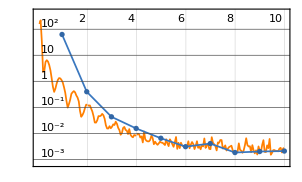
NetTrain Results
summary | ,,  batches:200  rounds:10  time:7.8min  examples/s:440
data | ,,  training examples:20000  validation examples:10000  processed examples:204800  skipped examples:0
method | ,,  ADAMoptimizer  batch size1024CPU
round | ,,  loss:2.7×10^-3
validation | ,,  loss:2.1×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

Number of bins: 5823

θ: {2.9698,2.9698,2.9698,2.9698,2.9698,2.9698,2.9698,2.9698,2.9698,2.9698,2.3573,2.3573,2.3573,2.3573,2.3573,2.3573,2.3573,2.3573,2.3573,2.3573,2.15207,2.15207,2.15207,2.15207,2.15207,2.15207,2.15207,2.15207,2.15207,2.15207,2.68409,2.68409,2.68409,2.68409,2.68409,2.68409,2.68409,2.68409,2.68409,2.68409,2.39768,2.39768,2.39768,2.39768,2.39768,2.39768,2.39768,2.39768,2.39768,2.39768,2.97685,2.97685,2.97685,2.97685,2.97685,2.97685,2.97685,2.97685,2.97685,2.97685,2.77257,2.77257,2.77257,2.77257,2.77257,2.77257,2.77257,2.77257,2.77257,2.77257,2.52178,2.52178,2.52178,2.52178,2.52178,2.52178,2.52178,2.52178,2.52178,2.52178,2.46848,2.46848,2.46848,2.46848,2.46848,2.46848,2.46848,2.46848,2.46848,2.46848,2.33746,2.33746,2.33746,2.33746,2.33746,2.33746,2.33746,2.33746,2.33746,2.33746,2.37003,2.37003,2.37003,2.37003,2.37003,2.37003,2.37003,2.37003,2.37003,2.37003,2.59796,2.59796,2.59796,2.59796,2.59796,2.59796,2.59796,2.59796,2.59796,2.59796,2.18689,2.18689,2.18689,2.18689,2.18689,2.18689,2.18689,2.18689,2.18689,2.18689,2.65408,2.65408,2.65408,2.65408,2.65408,2.65408,2.65408,2.65408,2.65408,2.65408,2.17057,2.17057,2.17057,2.17057,2.17057,2.17057,2.17057,2.17057,2.17057,2.17057,2.50418,2.50418,2.50418,2.50418,2.50418,2.50418,2.50418,2.50418,2.50418,2.50418,2.90657,2.90657,2.90657,2.90657,2.90657,2.90657,2.90657,2.90657,2.90657,2.90657,2.25315,2.25315,2.25315,2.25315,2.25315,2.25315,2.25315,2.25315,2.25315,2.25315,2.49112,2.49112,2.49112,2.49112,2.49112,2.49112,2.49112,2.49112,2.49112,2.49112,2.8429,2.8429,2.8429,2.8429,2.8429,2.8429,2.8429,2.8429,2.8429,2.8429}

θ̂: {2.99662,2.86988,3.0252,3.23641,3.02875,3.12783,2.9427,3.08573,3.12721,2.87327,2.34963,2.39814,2.35216,2.37958,2.31065,2.37786,2.32018,2.37269,2.32572,2.39676,2.17134,2.16119,2.16879,2.14909,2.19388,2.15149,2.14218,2.18352,2.18184,2.17862,2.70938,2.68433,2.70543,2.68947,2.62084,2.67562,2.72862,2.66426,2.67446,2.66964,2.38699,2.46009,2.45808,2.39797,2.35043,2.3909,2.45719,2.36532,2.43136,2.41165,3.06373,3.09467,3.00011,3.00846,2.91288,3.26782,2.85396,2.92826,3.04755,2.86559,2.82729,2.78815,2.74481,2.81058,2.80834,2.81784,2.86167,2.85448,2.85098,2.73596,2.52857,2.49469,2.48043,2.49501,2.51022,2.55294,2.46832,2.47411,2.47118,2.44829,2.43623,2.45174,2.53303,2.50954,2.48445,2.47284,2.44555,2.46714,2.46385,2.48359,2.34241,2.39871,2.29531,2.31944,2.388,2.33262,2.3359,2.30752,2.37045,2.41301,2.31685,2.46103,2.36582,2.44019,2.43909,2.35367,2.41307,2.43284,2.42087,2.32067,2.56227,2.64404,2.56056,2.575,2.60702,2.61408,2.62459,2.61791,2.62598,2.54452,2.19745,2.1977,2.3107,2.22378,2.15831,2.2397,2.13595,2.19366,2.17123,2.16376,2.67024,2.61356,2.58199,2.77095,2.69282,2.5857,2.67173,2.61579,2.67799,2.65454,2.15554,2.19605,2.12488,2.15129,2.20054,2.17384,2.21023,2.1726,2.13955,2.2273,2.4676,2.54825,2.48565,2.50117,2.53699,2.52452,2.4642,2.4428,2.44276,2.57811,2.9096,2.92435,2.83685,2.87565,2.85842,2.8379,2.84321,2.91118,2.84604,3.04692,2.21889,2.30022,2.3043,2.26235,2.31106,2.30593,2.31671,2.31982,2.30566,2.28639,2.47637,2.48265,2.4741,2.4917,2.45134,2.44834,2.46749,2.59078,2.48347,2.56489,2.86293,2.87282,2.84843,2.88409,2.78092,2.85514,2.82899,2.82137,2.8442,2.75005}

abs(θ-θ̂): {0.0268246,0.0999169,0.0553988,0.266613,0.0589472,0.158026,0.0271021,0.115928,0.157407,0.0965318,0.00766541,0.0408394,0.0051377,0.0222828,0.0466478,0.0205655,0.0371153,0.0153963,0.0315738,0.0394637,0.019267,0.00912276,0.0167207,0.00297365,0.0418157,0.000580877,0.00988826,0.0314483,0.0297717,0.0265531,0.025285,0.000236551,0.0213402,0.00537662,0.0632522,0.00847336,0.044524,0.0198319,0.00962945,0.0144522,0.0106882,0.0624123,0.0604006,0.000291908,0.0472445,0.00677291,0.0595127,0.0323528,0.0336815,0.0139759,0.0868834,0.117821,0.0232621,0.031607,0.0639697,0.290971,0.12289,0.0485894,0.0707055,0.111262,0.0547244,0.015578,0.0277531,0.0380104,0.0357778,0.0452723,0.0891077,0.0819156,0.0784128,0.0366089,0.00679391,0.0270823,0.041344,0.0267642,0.0115574,0.0311639,0.0534576,0.0476611,0.0505937,0.0734904,0.0322544,0.016741,0.0645414,0.0410536,0.0159698,0.0043536,0.0229353,0.00134365,0.00463574,0.015101,0.00495491,0.0612544,0.0421452,0.0180151,0.0505403,0.0048348,0.00155559,0.0299386,0.0329927,0.0755504,0.0531732,0.090998,0.00420826,0.0701626,0.0690594,0.0163562,0.0430422,0.0628141,0.0508402,0.0493576,0.0356906,0.0460846,0.0373957,0.0229538,0.00905823,0.0161254,0.0266354,0.0199482,0.028022,0.0534392,0.0105653,0.0108116,0.123812,0.0368957,0.0285816,0.0528121,0.0509372,0.00677585,0.0156534,0.0231233,0.0161593,0.0405202,0.0720942,0.116864,0.0387347,0.0683856,0.0176437,0.0382891,0.0239115,0.000460393,0.0150274,0.0254839,0.0456828,0.0192718,0.0299748,0.00327311,0.0396608,0.0020381,0.0310182,0.0567306,0.0365783,0.0440701,0.0185305,0.00301229,0.0328053,0.0203401,0.0399827,0.0613824,0.0614198,0.0739325,0.00303283,0.0177781,0.0697185,0.0309213,0.0481504,0.0686742,0.0633658,0.0046083,0.0605296,0.140348,0.0342592,0.0470663,0.0511521,0.00920308,0.0579053,0.0527829,0.0635554,0.0666717,0.0525075,0.03324,0.0147517,0.0084675,0.0170181,0.000580959,0.0397795,0.0427829,0.0236283,0.0996579,0.00765092,0.0737664,0.020028,0.02992,0.00552765,0.0411946,0.0619791,0.0122444,0.0139123,0.0215259,0.00129763,0.092851}

RMSE:0.0568089

```mathematica
{Θ, e} = RunExperiment[WaringYuleDistribution, {2,3}];
```

### Poisson distribution

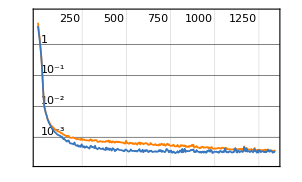
NetTrain Results
summary | ,,  batches:13420  rounds:1342  time:17s  examples/s:853115
data | ,,  training examples:10000  validation examples:5000  processed examples:13742080  skipped examples:0
method | ,,  ADAMoptimizer  batch size1024CPU
round | ,,  loss:3.74×10^-4
validation | ,,  loss:3.15×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

Number of bins: 17

θ: {2.43784,2.43784,2.43784,2.43784,2.43784,2.43784,2.43784,2.43784,2.43784,2.43784,2.59934,2.59934,2.59934,2.59934,2.59934,2.59934,2.59934,2.59934,2.59934,2.59934,2.99357,2.99357,2.99357,2.99357,2.99357,2.99357,2.99357,2.99357,2.99357,2.99357,2.90689,2.90689,2.90689,2.90689,2.90689,2.90689,2.90689,2.90689,2.90689,2.90689,2.36943,2.36943,2.36943,2.36943,2.36943,2.36943,2.36943,2.36943,2.36943,2.36943,2.94709,2.94709,2.94709,2.94709,2.94709,2.94709,2.94709,2.94709,2.94709,2.94709,2.32378,2.32378,2.32378,2.32378,2.32378,2.32378,2.32378,2.32378,2.32378,2.32378,2.03074,2.03074,2.03074,2.03074,2.03074,2.03074,2.03074,2.03074,2.03074,2.03074,2.30739,2.30739,2.30739,2.30739,2.30739,2.30739,2.30739,2.30739,2.30739,2.30739,2.23412,2.23412,2.23412,2.23412,2.23412,2.23412,2.23412,2.23412,2.23412,2.23412,2.17873,2.17873,2.17873,2.17873,2.17873,2.17873,2.17873,2.17873,2.17873,2.17873,2.93778,2.93778,2.93778,2.93778,2.93778,2.93778,2.93778,2.93778,2.93778,2.93778,2.39188,2.39188,2.39188,2.39188,2.39188,2.39188,2.39188,2.39188,2.39188,2.39188,2.8967,2.8967,2.8967,2.8967,2.8967,2.8967,2.8967,2.8967,2.8967,2.8967,2.92615,2.92615,2.92615,2.92615,2.92615,2.92615,2.92615,2.92615,2.92615,2.92615,2.09378,2.09378,2.09378,2.09378,2.09378,2.09378,2.09378,2.09378,2.09378,2.09378,2.24251,2.24251,2.24251,2.24251,2.24251,2.24251,2.24251,2.24251,2.24251,2.24251,2.02141,2.02141,2.02141,2.02141,2.02141,2.02141,2.02141,2.02141,2.02141,2.02141,2.47432,2.47432,2.47432,2.47432,2.47432,2.47432,2.47432,2.47432,2.47432,2.47432,2.12037,2.12037,2.12037,2.12037,2.12037,2.12037,2.12037,2.12037,2.12037,2.12037}

θ̂: {2.42328,2.4025,2.41913,2.41731,2.43668,2.4523,2.44361,2.43552,2.42214,2.42863,2.61738,2.63425,2.59935,2.57429,2.61327,2.61539,2.6155,2.60582,2.58267,2.62058,2.98493,2.99457,2.97451,3.0084,2.98956,2.99051,3.00068,2.96901,2.96535,2.98891,2.92384,2.89446,2.88529,2.90432,2.92076,2.90324,2.93548,2.89614,2.90019,2.91478,2.39092,2.37516,2.35353,2.31562,2.34515,2.39487,2.37106,2.37055,2.37287,2.36337,2.95139,2.94829,2.94822,2.94492,2.9458,2.96079,2.94713,2.97036,2.94336,2.93298,2.32008,2.32178,2.32721,2.31285,2.29434,2.32854,2.31465,2.33664,2.31257,2.3228,2.06168,2.0387,2.05137,2.05057,1.99131,2.03179,2.02772,2.01376,2.03989,2.03156,2.27847,2.30602,2.32746,2.29772,2.3138,2.30598,2.30766,2.30411,2.31093,2.27131,2.24611,2.23861,2.22344,2.21753,2.2434,2.22902,2.24703,2.22056,2.24557,2.2224,2.16014,2.17536,2.21563,2.17503,2.1915,2.18428,2.18173,2.17437,2.17078,2.18723,2.94641,2.90322,2.96009,2.91762,2.92735,2.94103,2.93995,2.93785,2.92736,2.94004,2.40566,2.42901,2.39414,2.42555,2.40622,2.42709,2.36075,2.38972,2.3942,2.37747,2.91627,2.88656,2.86512,2.89123,2.86239,2.90215,2.88108,2.89639,2.90161,2.87159,2.94399,2.94826,2.95118,2.91549,2.92053,2.93229,2.93358,2.9519,2.92853,2.92734,2.10486,2.09379,2.07742,2.11179,2.10052,2.09421,2.09346,2.07823,2.11608,2.0892,2.22569,2.2524,2.24898,2.23702,2.27007,2.22389,2.21056,2.22825,2.22848,2.25654,2.05066,2.03095,2.01026,2.03055,1.9951,2.04945,2.02933,2.01517,2.01136,2.04631,2.4714,2.50596,2.4776,2.45071,2.48382,2.47028,2.46563,2.47983,2.46018,2.5049,2.13006,2.1166,2.12977,2.09578,2.11655,2.09544,2.1095,2.10799,2.11748,2.14618}

abs(θ-θ̂): {0.0145588,0.0353394,0.0187137,0.0205352,0.001158,0.0144579,0.00576878,0.00232243,0.0157042,0.00921726,0.0180419,0.0349105,0.0000103489,0.0250417,0.0139309,0.016059,0.0161689,0.00648961,0.0166685,0.021241,0.008641,0.000997791,0.0190596,0.0148351,0.00400447,0.00306081,0.00711561,0.0245604,0.0282161,0.00465511,0.0169521,0.012431,0.021592,0.00256432,0.0138758,0.00364674,0.0285922,0.0107502,0.0066935,0.00789581,0.0214824,0.00572936,0.0159071,0.0538152,0.0242828,0.0254325,0.00162117,0.00111763,0.00343268,0.00606759,0.00429205,0.00119476,0.00112562,0.00217529,0.00129266,0.0136998,0.0000384266,0.0232659,0.00373526,0.0141124,0.00370138,0.00199549,0.00343497,0.0109338,0.029436,0.00475771,0.0091254,0.0128601,0.0112085,0.00098007,0.0309403,0.00795559,0.0206259,0.0198281,0.0394362,0.00104455,0.00301762,0.0169856,0.00915317,0.000822108,0.0289255,0.00136721,0.0200714,0.00967514,0.00640953,0.00140988,0.000269059,0.00327885,0.00354255,0.0360819,0.0119886,0.00448271,0.0106864,0.0165885,0.00927587,0.00510077,0.0129103,0.013567,0.0114429,0.0117195,0.0185971,0.00337745,0.0369003,0.00370575,0.0127704,0.00555037,0.00299882,0.00436212,0.00794984,0.00850104,0.00863561,0.0345558,0.0223151,0.0201592,0.0104243,0.00325784,0.00217327,0.0000782876,0.0104133,0.00226864,0.0137892,0.0371356,0.00226474,0.0336781,0.0143456,0.0352108,0.0311213,0.00215006,0.00232935,0.0144029,0.0195622,0.0101454,0.0315869,0.00547434,0.034317,0.00545143,0.0156262,0.000317589,0.00491021,0.0251088,0.0178411,0.0221079,0.0250275,0.0106606,0.00562071,0.00613548,0.00743319,0.0257487,0.00238015,0.0011933,0.0110771,7.05227×10^-6,0.0163654,0.0180081,0.00674047,0.000425238,0.000327926,0.015556,0.0222982,0.0045806,0.0168196,0.00988447,0.0064677,0.0054909,0.0275587,0.0186254,0.0319484,0.0142595,0.014033,0.0140237,0.0292476,0.0095414,0.0111459,0.00914252,0.0263066,0.028037,0.00792254,0.00623571,0.0100516,0.0248956,0.00292097,0.0316383,0.00328435,0.0236102,0.00949611,0.00403987,0.00868855,0.00550594,0.0141364,0.0305835,0.00968772,0.00376886,0.00939566,0.0245885,0.00382226,0.0249359,0.0108725,0.0123817,0.00289792,0.025811}

RMSE:0.0166026

```mathematica
{Θ, e} = RunExperiment[PoissonDistribution, {2,3}];
```

### Geometric distribution

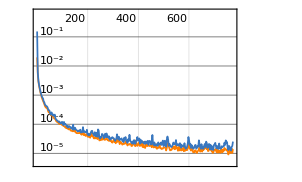
NetTrain Results
summary | ,,  batches:7740  rounds:774  time:25s  examples/s:318191
data | ,,  training examples:10000  validation examples:5000  processed examples:7925760  skipped examples:0
method | ,,  ADAMoptimizer  batch size1024CPU
round | ,,  loss:1.6×10^-5
validation | ,,  loss:3.52×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

Number of bins: 71

θ: {0.291991,0.291991,0.291991,0.291991,0.291991,0.291991,0.291991,0.291991,0.291991,0.291991,0.288498,0.288498,0.288498,0.288498,0.288498,0.288498,0.288498,0.288498,0.288498,0.288498,0.290482,0.290482,0.290482,0.290482,0.290482,0.290482,0.290482,0.290482,0.290482,0.290482,0.252793,0.252793,0.252793,0.252793,0.252793,0.252793,0.252793,0.252793,0.252793,0.252793,0.235716,0.235716,0.235716,0.235716,0.235716,0.235716,0.235716,0.235716,0.235716,0.235716,0.292436,0.292436,0.292436,0.292436,0.292436,0.292436,0.292436,0.292436,0.292436,0.292436,0.236559,0.236559,0.236559,0.236559,0.236559,0.236559,0.236559,0.236559,0.236559,0.236559,0.264002,0.264002,0.264002,0.264002,0.264002,0.264002,0.264002,0.264002,0.264002,0.264002,0.265668,0.265668,0.265668,0.265668,0.265668,0.265668,0.265668,0.265668,0.265668,0.265668,0.201777,0.201777,0.201777,0.201777,0.201777,0.201777,0.201777,0.201777,0.201777,0.201777,0.206199,0.206199,0.206199,0.206199,0.206199,0.206199,0.206199,0.206199,0.206199,0.206199,0.215372,0.215372,0.215372,0.215372,0.215372,0.215372,0.215372,0.215372,0.215372,0.215372,0.222461,0.222461,0.222461,0.222461,0.222461,0.222461,0.222461,0.222461,0.222461,0.222461,0.280849,0.280849,0.280849,0.280849,0.280849,0.280849,0.280849,0.280849,0.280849,0.280849,0.208337,0.208337,0.208337,0.208337,0.208337,0.208337,0.208337,0.208337,0.208337,0.208337,0.212158,0.212158,0.212158,0.212158,0.212158,0.212158,0.212158,0.212158,0.212158,0.212158,0.20562,0.20562,0.20562,0.20562,0.20562,0.20562,0.20562,0.20562,0.20562,0.20562,0.288871,0.288871,0.288871,0.288871,0.288871,0.288871,0.288871,0.288871,0.288871,0.288871,0.237105,0.237105,0.237105,0.237105,0.237105,0.237105,0.237105,0.237105,0.237105,0.237105,0.236875,0.236875,0.236875,0.236875,0.236875,0.236875,0.236875,0.236875,0.236875,0.236875}

θ̂: {0.28875,0.295366,0.290166,0.294492,0.29026,0.290928,0.294069,0.292114,0.293386,0.285926,0.289129,0.290179,0.282462,0.290308,0.290068,0.284093,0.281089,0.293391,0.283229,0.292681,0.290662,0.288726,0.294349,0.29351,0.291458,0.292784,0.293079,0.285689,0.292234,0.293555,0.253022,0.245083,0.25636,0.254856,0.249414,0.254796,0.255216,0.258655,0.249131,0.249416,0.237782,0.232463,0.235668,0.236513,0.234925,0.240249,0.235817,0.232577,0.235082,0.244269,0.289042,0.2964,0.293252,0.293958,0.29438,0.292723,0.293484,0.294843,0.289312,0.290409,0.240337,0.233831,0.227329,0.236044,0.232891,0.234486,0.234369,0.244063,0.232731,0.240512,0.26237,0.264933,0.270593,0.264832,0.265682,0.266009,0.262348,0.268796,0.2659,0.265871,0.264402,0.26617,0.262613,0.264519,0.257242,0.267816,0.26204,0.258075,0.271257,0.265325,0.204091,0.206334,0.204513,0.202548,0.205952,0.207586,0.206493,0.205281,0.204785,0.203574,0.210147,0.211028,0.20755,0.209632,0.209408,0.207314,0.207829,0.206033,0.21046,0.206698,0.219336,0.219271,0.216139,0.216064,0.215016,0.21884,0.217178,0.219323,0.217389,0.2166,0.224513,0.224759,0.221463,0.222708,0.224422,0.222452,0.223333,0.223303,0.225056,0.222548,0.283379,0.281762,0.282104,0.28326,0.278328,0.282811,0.28455,0.278599,0.284277,0.283245,0.209096,0.207148,0.209455,0.210483,0.209163,0.214592,0.211561,0.208388,0.212834,0.210592,0.212621,0.212631,0.213498,0.214447,0.212236,0.215179,0.21305,0.213435,0.215742,0.214896,0.208779,0.211279,0.205172,0.209954,0.20918,0.207702,0.206732,0.207501,0.209776,0.210084,0.289864,0.289694,0.287646,0.286492,0.286387,0.290375,0.29274,0.286367,0.287376,0.288712,0.235893,0.242348,0.233012,0.230417,0.233243,0.235106,0.236878,0.238654,0.238658,0.23591,0.240527,0.237577,0.234512,0.232902,0.245055,0.238963,0.232806,0.236962,0.23686,0.240422}

abs(θ-θ̂): {0.00324089,0.00337543,0.00182477,0.00250109,0.00173072,0.00106317,0.00207769,0.000123166,0.00139531,0.0060652,0.00063028,0.0016806,0.00603623,0.00180983,0.0015701,0.00440506,0.00740911,0.00489228,0.00526969,0.00418227,0.000180309,0.00175568,0.00386751,0.00302762,0.000976061,0.00230247,0.00259668,0.00479271,0.00175205,0.00307349,0.000229532,0.00771015,0.00356727,0.00206375,0.00337834,0.00200334,0.00242286,0.00586181,0.00366127,0.00337625,0.00206626,0.00325325,0.0000480965,0.000796993,0.000790577,0.00453316,0.000101452,0.00313857,0.000633563,0.00855285,0.00339392,0.00396457,0.000815924,0.00152278,0.00194436,0.000287111,0.00104817,0.00240758,0.00312391,0.00202617,0.00377778,0.00272808,0.00922989,0.000514872,0.00366784,0.00207335,0.00218964,0.00750456,0.00382834,0.00395288,0.00163209,0.000931145,0.0065912,0.000830145,0.00167966,0.00200665,0.00165421,0.00479376,0.00189772,0.00186873,0.00126595,0.000501952,0.00305519,0.00114874,0.00842644,0.00214796,0.00362776,0.00759367,0.00558858,0.000342825,0.00231325,0.00455701,0.00273523,0.00077094,0.00417489,0.00580853,0.00471529,0.00350346,0.0030072,0.00179636,0.00394759,0.0048286,0.00135097,0.00343298,0.00320864,0.00111492,0.0016298,0.000166235,0.00426045,0.000498864,0.00396357,0.00389911,0.000766674,0.000691334,0.000356412,0.00346758,0.00180549,0.0039509,0.00201715,0.00122761,0.00205183,0.002298,0.000997678,0.000247254,0.00196108,9.20966×10^-6,0.000871509,0.000841676,0.00259471,0.0000867985,0.00253063,0.000913019,0.00125551,0.00241133,0.00252098,0.00196167,0.00370129,0.0022496,0.0034281,0.00239568,0.000759472,0.00118897,0.0011177,0.0021462,0.000826319,0.00625487,0.00322442,0.0000507881,0.00449741,0.00225513,0.000463377,0.000473167,0.00133958,0.00228917,0.0000777205,0.00302086,0.000891965,0.00127755,0.00358362,0.00273768,0.00315882,0.00565823,0.00044833,0.00433314,0.00355969,0.00208114,0.00111143,0.00188071,0.00415573,0.0044639,0.000992841,0.000822759,0.00122535,0.00237876,0.00248432,0.00150359,0.00386918,0.00250467,0.00149544,0.000159466,0.00121179,0.00524323,0.0040925,0.0066875,0.00386217,0.00199862,0.00022715,0.0015491,0.00155331,0.00119459,0.00365198,0.000702246,0.00236271,0.00397293,0.00817998,0.00208793,0.00406827,0.0000875137,0.00001444,0.00354716}

RMSE:0.00321971

```mathematica
{Θ, e} = RunExperiment[GeometricDistribution, {0.2,0.3}];
```